```mathematica
Zeta[0]
```

-1/2

```mathematica
Zeta'[0]
```

-1/2 Log[2 π]

```mathematica
ContourPlot3D[{x^2+y^2-z^2==0.001,z+x},{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

```mathematica
12(2/3+3/2)
```

26

```mathematica
3200-1400-1000
```

800

```mathematica
15 7
50+12 5
```

105

110

```mathematica
NIntegrate[(x^3 Cos[x/2]+1/2)Sqrt[4-x^2],{x,-2,2}]
```

3.14159

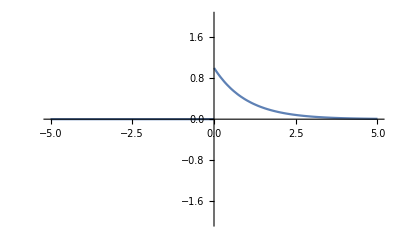

```mathematica
Plot[Exp[-x]  HeavisideTheta[x],{x,-5,5},PlotRange->2]
```

```mathematica
Series[-Log[1-x],{x,0,5}]
```

x+x^2/2+x^3/3+x^4/4+x^5/5+O[x]^6

```mathematica
Sqrt[Conjugate[z]]==Conjugate[Sqrt[z]]/.z->2.-3I
```

True

```mathematica
√(2-ⅈ)//N
Conjugate[√(2+ⅈ)]//N
```

1.45535-0.343561 ⅈ

1.45535-0.343561 ⅈ

```mathematica
Sqrt[w/z]==Sqrt[w]/Sqrt[z]/.w->-I+.1/.z->I
```

True

```mathematica
2 ArcTanh[x]
```

2 ArcTanh[x]

```mathematica
TrigToExp[2 ArcTanh[x]]
```

-Log[1-x]+Log[1+x]

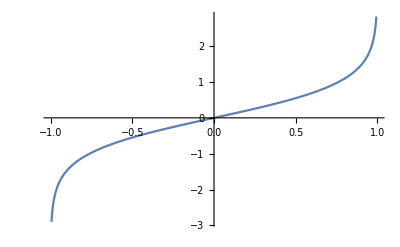

```mathematica
Plot[ArcTanh[x],{x,-1,1}]
```

```mathematica
Log[(z-I)/(z+I)-(w-I)/(w+I)]+Log[(z-I)/(z+I)+(w-I)/(w+I)]//Simplify
```

Log[-(2 ⅈ (w-z))/((ⅈ+w) (ⅈ+z))]+Log[(2 (1+w z))/((ⅈ+w) (ⅈ+z))]

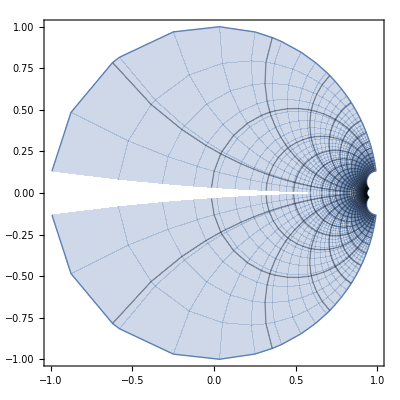

```mathematica
ParametricPlot[{Re[(#-I)/(#+I)],Im[(#-I)/(#+I)]}&[x+I y],{x,-15,15},{y,0,30},PlotRange->1,PlotPoints->30,PerformanceGoal->"Quality",Mesh->{30,30},WorkingPrecision->20]
```

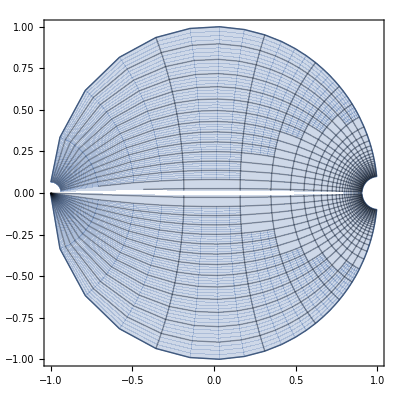

```mathematica
ParametricPlot[{Re[(#-I)/(#+I)],Im[(#-I)/(#+I)]}&[r Exp[I θ]],{r,0,20},{θ,0,Pi},PlotRange->1,PlotPoints->30,Mesh->Full,WorkingPrecision->30]
```

```mathematica
(z-I)/(z+I)-(w-I)/(w+I)
```

-(-ⅈ+w)/(ⅈ+w)+(-ⅈ+z)/(ⅈ+z)

```mathematica
D[(z-I)/(z+I),z]//Simplify
```

(2 ⅈ)/(ⅈ+z)^2

```mathematica
I(1+x)/(1-x)-I(1+y)/(1-y)//Simplify
I(1+x)/(1-x)+I(1+y)/(1-y)//Simplify
```

(2 ⅈ (x-y))/((-1+x) (-1+y))

-(2 ⅈ (-1+x y))/((-1+x) (-1+y))

```mathematica
D[D[Log[1-x by],x],by]//Simplify
D[D[Log[x-y],x],y]//Simplify
```

-1/(-1+by x)^2

1/(x-y)^2

```mathematica
D[D[Log[Sqrt[z]-Sqrt[w]]-Log[Sqrt[z]+Sqrt[w]],z],w]//Simplify
```

(w+z)/(2 √w (w-z)^2 √z)

```mathematica
1/(z1-z2)D[1/(z2-z3)^(2Δ),z2]+1/(z1-z3)D[1/(z2-z3)^(2Δ),z3]+Δ/(z1-z2)^2 1/(z2-z3)^(2Δ)+Δ/(z1-z3)^2 1/(z2-z3)^(2Δ)//Simplify
```

((z2-z3)^(2-2 Δ) Δ)/((z1-z2)^2 (z1-z3)^2)

```mathematica
Series[D[(z+w)/(2 Sqrt[z w] (z-w)),w]-1/(z-w)^2,{z,w,1}]
```

(-1+w/(√(w^2)))/(z-w)^2-1/(8 (w √(w^2)))+O[z-w]^2

```mathematica
Series[z^2 1/(z-w)^2,{w,0,5}]
```

1+(2 w)/z+(3 w^2)/z^2+(4 w^3)/z^3+(5 w^4)/z^4+(6 w^5)/z^5+O[w]^6

```mathematica
Series[(1/2)/(z-w)^4,{w,0,5}]
```

1/(2 z^4)+(2 w)/z^5+(5 w^2)/z^6+(10 w^3)/z^7+(35 w^4)/(2 z^8)+(28 w^5)/z^9+O[w]^6

```mathematica
D[1/(z-w),z]
```

-1/(-w+z)^2

```mathematica
Sum[1/(k-1/2) (w/z)^(k-1/2),{k,1,Infinity}]
```

(2 √w ArcTanh[(√w)/(√z)])/(√(w/z) √z)

```mathematica
Assuming[Im[w]>0&&Im[z]>0,Simplify[(2 √w)/(√(w/z) √z)]]
Simplify[(2 √w ArcTanh[(√w)/(√z)])/(√(w/z) √z)]
```

(2 √(w/z) √z)/(√w)

(2 √(w/z) √z ArcTanh[(√w)/(√z)])/(√w)

```mathematica
TrigToExp[(2 √w ArcTanh[(√w)/(√z)])/(√(w/z) √z)]
```

-(√w Log[1-(√w)/(√z)])/(√(w/z) √z)+(√w Log[1+(√w)/(√z)])/(√(w/z) √z)

```mathematica
Sum[1/(k+1/2) w^(k+1/2),{k,0,Infinity}]
```

2 ArcTanh[√w]

```mathematica
TrigToExp[2 ArcTanh[√w]]
```

-Log[1-√w]+Log[1+√w]

```mathematica
TrigToExp[2 ArcTanh[√w]]
```

-Log[1-√w]+Log[1+√w]

```mathematica
TrigToExp[(2 √(w/z) √z ArcTanh[(√w)/(√z)])/(√w)]
```

-(√(w/z) √z Log[1-(√w)/(√z)])/(√w)+(√(w/z) √z Log[1+(√w)/(√z)])/(√w)

```mathematica
√(w/z) √z/√w/.z->I/.w->-I
```

-1

```mathematica
-Log[1-√w]+Log[1+√w]/.w->w/z
```

-Log[1-√(w/z)]+Log[1+√(w/z)]